# MathIOmica Toolbox Protocols

## MathIOmica Installation Instructions

## Dynamic Transcriptome Analysis Protocol

## Import MathIOmica Package

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
<<MathIOmica`
```

MathIOmica (https://mathiomica.org), by [G. Mias Lab](http://georgemias.org)

## Obtain Data and Create OmicsObject

### Option 1: Create OmicsObject from imported CSV File

#### Import Data

```mathematica
inputData=Import["./inputData.csv","CSV"]
```

{{ID,P1011116H08,P1021516H08,P1031416H08,P1040615H08,P1041315H08,P1042015H08,P1042715H08,P1050415H08,P1051115H08,P1051815H08,79,P1070415H08,P1070515H08,P1070615H08,P1070715H08,P1071315H08,P1072015H08,P1081015H08,P1091415H08,P1101215H08,P1110915H08,P1120715H08},84646,{1}}
 |  |  |  |

```mathematica
dataPoints=Query[1,2;;]@inputData
```

{P1011116H08,P1021516H08,P1031416H08,P1040615H08,P1041315H08,P1042015H08,P1042715H08,P1050415H08,P1051115H08,P1051815H08,P1052515H07,P1052515H08,P1052515H09,P1052515H10,P1052515H11,P1052515H12,P1052515H13,P1052515H14,P1052515H15,P1052515H16,P1052515H17,P1052515H18,P1052515H19,P1052515H20,P1052515H21,P1052515H22,P1052515H23,P1052515H24,P1052615H01,P1052615H02,P1052615H03,P1052615H04,P1052615H05,P1052615H06,P1052615H07,P1052615H08,P1060215H08,P1060515H08,P1060615H08,P1060715H07,P1060715H08,P1060715H09,P1060715H10,P1060715H11,P1060715H12,P1060715H13,P1060715H14,P1060715H15,P1060715H16,P1060715H17,P1060715H18,P1060715H19,P1060715H20,P1060715H21,P1060715H22,P1060715H23,P1060715H24,P1060815H01,P1060815H02,P1060815H03,P1060815H04,P1060815H05,P1060815H06,P1060815H08,P1060915H08,P1061015H08,P1061115H08,P1061215H08,P1061315H08,P1061415H08,P1061515H08,P1061615H08,P1061715H08,P1061815H08,P1061915H08,P1062015H08,P1062115H08,P1062215H08,P1062315H08,P1062415H08,P1062515H08,P1062615H08,P1062715H08,P1062815H08,P1062915H08,P1063015H08,P1070115H08,P1070215H08,P1070315H08,P1070415H08,P1070515H08,P1070615H08,P1070715H08,P1071315H08,P1072015H08,P1081015H08,P1091415H08,P1101215H08,P1110915H08,P1120715H08}

#### Create OmicsObject

```mathematica
innerLabelsPerSet=StringSplit[#,":"]&/@inputData[[2;;,1]];
```

```mathematica
measurements=ConstantArray[innerLabelsPerSet,Length[dataPoints]];
```

```mathematica
expression={#}&/@#&/@Transpose[inputData[[2;;,2;;]]];
```

```mathematica
metadata=ConstantArray[{"RNA"},{Length[dataPoints],Length[innerLabelsPerSet]}];
```

```mathematica
expressionOO=OmicsObjectCreator[dataPoints,measurements,expression,metadata];
```

```mathematica
Query[{1,2},{1,2,3}]@expressionOO
```

<|P1011116H08→<|{A1BG-AS1,antisense}→{{0},{RNA}},{A1BG,processed_transcript}→{{10.2086},{RNA}},{A1BG,protein_coding}→{{0},{RNA}}|>,P1021516H08→<|{A1BG-AS1,antisense}→{{3.16499},{RNA}},{A1BG,processed_transcript}→{{2.29604},{RNA}},{A1BG,protein_coding}→{{0},{RNA}}|>|>

```mathematica
Query[{"P1061715H08","P1062315H08"},{Key[{"NFKB1","protein_coding"}],Key[{"A1BG","processed_transcript"}]}]@expressionOO
```

<|P1061715H08→<|{NFKB1,protein_coding}→{{427.859},{RNA}},{A1BG,processed_transcript}→{{2.08629},{RNA}}|>,P1062315H08→<|{NFKB1,protein_coding}→{{366.214},{RNA}},{A1BG,processed_transcript}→{{0},{RNA}}|>|>

#### Save OmicsObject for later use

Export as optimized version:

```mathematica
DumpSave["./expressionOO.mx",expressionOO];
```

### Option 2: Import from previously saved OmicsObject (**After Option 1 has been ran previously**)

```mathematica
<<"./expressionOO.mx"
```

### Subset Data to use

```mathematica
assignment=<|"P1060515H08"->"-2","P1060615H08"->"-1","P1060715H08"->"0","P1060815H08"->"1","P1060915H08"->"2","P1061015H08"->"3","P1061115H08"->"4","P1061215H08"->"5","P1061315H08"->"6","P1061415H08"->"7","P1061515H08"->"8","P1061615H08"->"9","P1061715H08"->"10","P1061815H08"->"11","P1061915H08"->"12","P1062015H08"->"13","P1062115H08"->"14","P1062215H08"->"15","P1062315H08"->"16","P1062415H08"->"17","P1062515H08"->"18","P1062615H08"->"19","P1062715H08"->"20","P1062815H08"->"21","P1062915H08"->"22","P1063015H08"->"23","P1070115H08"->"24","P1070215H08"->"25","P1070315H08"->"26","P1070415H08"->"27","P1070515H08"->"28","P1070615H08"->"29","P1070715H08"->"30"|>;
```

```mathematica
expressioOOSubset=KeyMap[assignment]@Query[Keys@assignment]@expressionOO
```

<|-2→<|{A1BG-AS1,antisense}→{{95.4815},{RNA}},{A1BG,processed_transcript}→{{0},{RNA}},{A1BG,protein_coding}→{{0},{RNA}},84642,{ZZZ3,processed_transcript}→{{210.392},{RNA}},{ZZZ3,protein_coding}→{{0.718926},{RNA}}|>,-1→<|1|>,29,29→1,30→<|1|>|>
 |  |  |  |

## Transcriptome Data Analysis Using Autocorrelations

### Tag Missing and Low Values

```mathematica
RNAzeroTag=LowValueTag[expressioOOSubset,0];
RNAAdjusted=LowValueTag[RNAzeroTag,1,ValueReplacement-> 1];
```

```mathematica
timesReferencesRNA=Keys[RNAAdjusted]
```

{-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

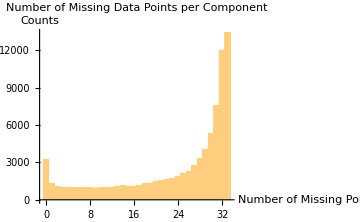

{Missing -> Counts: ,<|0→3196,1→1280,2→1079,3→1016,4→1008,5→970,6→961,7→970,8→953,9→943,10→980,11→1010,12→988,13→1096,14→1119,15→1093,16→1106,17→1160,18→1295,19→1345,20→1462,21→1530,22→1664,23→1730,24→1875,25→2122,26→2294,27→2748,28→3305,29→4051,30→5333,31→7568,32→12009,33→13388|>}

-Graphics-

```mathematica
RNAFiltered=FilterMissing[RNAAdjusted,3/4,Reference-> timesReferencesRNA[[3]]];
```

### Create Transcriptome Time Series

```mathematica
timesRNA=TimeExtractor[RNAFiltered]
```

{-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
TimeSeriesRNA=CreateTimeSeries[RNAFiltered]
```

<|{A2M,protein_coding}→{12.7545,Missing[],Missing[],Missing[],1.14687,8.11379,Missing[],1.35458,364.18,15,353.81,36.7626,29.7771,72.3165,42.9579,21.3693,60.6157,36.6882,65.9137},11432|>
 |  |  |  |

```mathematica
RNABaseline=SeriesInternalCompare[TimeSeriesRNA,ComparisonIndex-> 3]
```

<|{A2ML1,protein_coding}→{-680.775,2480.63,0.,-1557.23,28.5876,184.139,2744.72,-1216.49,2377.73,2322.75,-659.912,-538.611,-343.38,-109.272,-943.515,954.499,870.256,-480.063,-71.2808,136.693,-705.978,322.772,-244.693,248.436,216.788,725.096,-898.767,-875.402,-682.59,-501.,-793.04,-1189.79,-660.224},8153,{1}→1|>
 |  |  |  |

```mathematica
NormedRNA=SeriesApplier[Normalize,RNABaseline];
```

```mathematica
normedRNAClean=ConstantSeriesClean[NormedRNA];
```

```mathematica
Length[normedRNAClean]
```

8155

### Resampling Transcriptome Data

```mathematica
RNABootstrap=BootstrapGeneral[RNAFiltered,100000];
```

#### Processing Bootstrap Transcriptome Data;

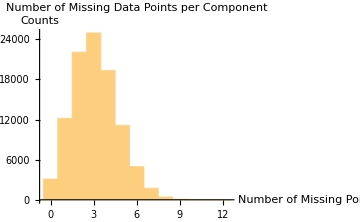

{Missing -> Counts: ,<|0→3101,1→12180,2→22066,3→24955,4→19338,5→11126,6→4968,7→1721,8→427,9→92,10→21,11→4,12→1|>}

-Graphics-

```mathematica
RNABtFiltered=FilterMissing[RNABootstrap,3/4,Reference-> "0"];
```

```mathematica
TimeSeriesBtRNA=CreateTimeSeries[RNABtFiltered];
```

```mathematica
RNABaselineBt=SeriesInternalCompare[TimeSeriesBtRNA,ComparisonIndex-> 3];
```

```mathematica
normedRNABt=SeriesApplier[Normalize,RNABaselineBt];
```

```mathematica
normedRNACleanBt=ConstantSeriesClean[normedRNABt];
```

### Classification of Transcriptome Data Autocorrelation

#### Quantile 0.99 Cutoff Generation

```mathematica
q99RNAauto=QuantileEstimator[normedRNACleanBt,timesRNA,Method-> "Autocorrelation",QuantileValue-> .99]
```

{0.162193,0.788084,0.399994,0.672312,0.475071,0.635303,0.508849,0.59773,0.515424,0.548407,0.493415,0.502878,0.427653,0.449192,0.382212,0.413728}

```mathematica
q99RNASpikes=QuantileEstimator[normedRNACleanBt,timesRNA,Method-> "Spikes",QuantileValue-> .99]
```

<|27→{0.999983,-0.262922},31→{0.999981,-0.240415},33→{0.999977,-0.229213},30→{0.99998,-0.24388},32→{0.999974,-0.235534},29→{0.999973,-0.249773},28→{0.999981,-0.257296},26→{0.999969,-0.27618},25→{0.999919,-0.268048}|>

#### Times Series Classification

```mathematica
RNAClassification=TimeSeriesClassification[normedRNAClean,timesRNA,AutocorrelationCutoffs-> q99RNAauto,SpikeCutoffs->q99RNASpikes,Method-> "Autocorrelation"];
```

Method → "Autocorrelation"

```mathematica
Query[All,Length]@RNAClassification
```

<|SpikeMax→2,SpikeMin→2261,Lag1→433,Lag2→110,Lag3→123,Lag4→103,Lag5→92,Lag6→49,Lag7→99,Lag8→31,Lag9→25,Lag10→29,Lag11→98,Lag12→44,Lag13→34,Lag14→58,Lag15→68,Lag16→72|>

#### Group/Subgroup Cluster Generation

```mathematica
RNAClusters=TimeSeriesClusters[RNAClassification];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

#### Dendrogram / Heatmap Generation

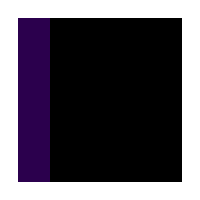
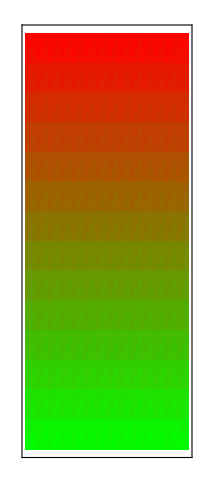
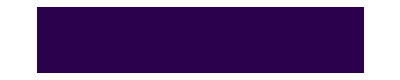
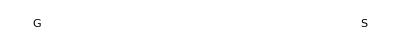
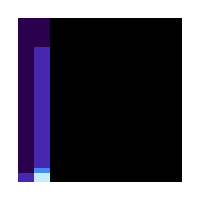
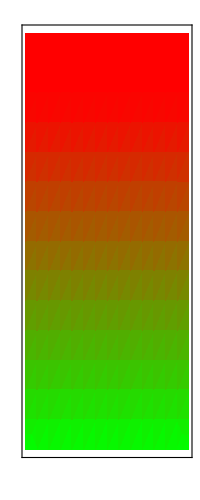
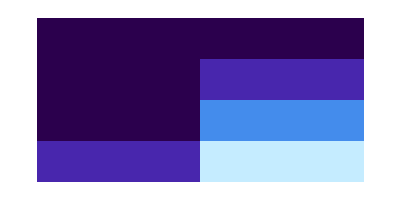
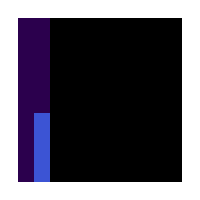
SpikeMax
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


SpikeMin
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag1
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag2
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag3
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag4
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag5
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag6
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag7
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag8
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag9
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag10
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag11
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag12
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag13
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag14
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag15
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  | 


Lag16
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  |

```mathematica
outputHeatmaps=TimeSeriesDendrogramsHeatmaps[RNAClusters]
```

```mathematica
outputHeatmaps[[1,3]]
```

Lag1
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Time (arbitrary units) |  |  |

## Annotation and Enrichment

### Gene Ontology Analysis

We can carry out Gene Ontology analysis for all the classes and groups/subgroups.:

```mathematica
goAnalysis=GOAnalysis[RNAClusters,OntologyLengthFilter-> 3,ReportFilter-> 3 ];
```

```mathematica
Query[All,All,Length]@goAnalysis
```

<|SpikeMax→<|G1S1→0|>,SpikeMin→<|G1S1→82,G1S2→491,G1S3→9,G2S1→31|>,Lag1→<|G1S1→107,G1S2→75,G2S1→0|>,Lag2→<|G1S1→0,G1S2→3,G2S1→0,G2S2→0|>,Lag3→<|G1S1→4,G1S2→8,G1S3→1|>,Lag4→<|G1S1→1,G1S2→0,G2S1→0|>,Lag5→<|G1S1→1,G1S2→5,G2S1→0|>,Lag6→<|G1S1→1,G2S1→0,G2S2→0|>,Lag7→<|G1S1→0,G1S2→0,G2S1→2,G2S2→0|>,Lag8→<|G1S1→2,G1S2→1,G2S1→0|>,Lag9→<|G1S1→4,G2S1→0|>,Lag10→<|G1S1→0,G1S2→0,G1S3→0,G1S4→0,G1S5→0,G1S6→0,G2S1→0|>,Lag11→<|G1S1→5,G1S2→2,G2S1→0|>,Lag12→<|G1S1→0,G1S2→2,G2S1→0|>,Lag13→<|G1S1→4,G1S2→0|>,Lag14→<|G1S1→0,G2S1→0|>,Lag15→<|G1S1→1,G1S2→2|>,Lag16→<|G1S1→2,G1S2→0,G2S1→0|>|>

```mathematica
bpResults=Query["Lag1","G1S1",Select[#[[3,1,2]]=="biological_process"&]]@goAnalysis
```

<|GO:0019221→{{7.58844×10^-8,0.0000384923,True},{214,281,19772,16},{{cytokine-mediated signaling pathway,biological_process},{{{JAK3,protein_coding}},{{ITGAX,protein_coding}},{{STAT1,protein_coding}},{{JAK3,processed_transcript}},{{CSF3R,retained_intron}},{{IL1B,retained_intron}},{{IL4R,retained_intron}},{{IL1RN,retained_intron}},{{IL1B,processed_transcript}},{{MCL1,protein_coding}},{{BCL6,processed_transcript}},{{BCL6,protein_coding}},{{ITGAM,retained_intron}},{{IRAK2,protein_coding}},{{IL1R1,protein_coding}},{{ZEB1,protein_coding}}}}},GO:0045626→{{1.25038×10^-6,0.000376979,True},{214,3,19772,3},{{negative regulation of T-helper 1 cell differentiation,biological_process},{{{JAK3,protein_coding}},{{JAK3,processed_transcript}},{{IL4R,retained_intron}}}}},GO:0070487→{{1.25038×10^-6,0.000376979,True},{214,3,19772,3},{{monocyte aggregation,biological_process},{{{IL1B,retained_intron}},{{IL1B,processed_transcript}},{{CD44,protein_coding}}}}},GO:0070555→{{1.30057×10^-6,0.000376979,True},{214,33,19772,6},{{response to interleukin-1,biological_process},{{{CYBA,retained_intron}},{{IL1B,retained_intron}},{{SRC,protein_coding}},{{IL1B,processed_transcript}},{{IRAK2,protein_coding}},{{IL1R1,protein_coding}}}}},GO:2001243→{{3.21282×10^-6,0.000769128,True},{214,22,19772,5},{{negative regulation of intrinsic apoptotic signaling pathway,biological_process},{{{PPIF,nonsense_mediated_decay}},{{BCL2L2,protein_coding}},{{SRC,protein_coding}},{{MCL1,protein_coding}},{{IVNS1ABP,protein_coding}}}}},GO:0035771→{{4.9615×10^-6,0.000987019,True},{214,4,19772,3},{{interleukin-4-mediated signaling pathway,biological_process},{{{JAK3,protein_coding}},{{JAK3,processed_transcript}},{{IL4R,retained_intron}}}}},GO:0043312→{{5.35101×10^-6,0.000987019,True},{214,481,19772,18},{{neutrophil degranulation,biological_process},{{{CTSB,retained_intron}},{{CAPN1,protein_coding}},{{TOM1,nonsense_mediated_decay}},{{PKM,protein_coding}},{{STK10,processed_transcript}},{{CYBA,retained_intron}},{{FTH1,nonsense_mediated_decay}},{{ITGAX,protein_coding}},{{ADAM8,protein_coding}},{{SLC2A3,retained_intron}},{{DNAJC5,protein_coding}},{{CD44,protein_coding}},{{LTA4H,protein_coding}},{{MAN2B1,retained_intron}},{{COTL1,processed_transcript}},{{ITGAM,retained_intron}},{{DIAPH1,protein_coding}},{{AMPD3,protein_coding}}}}},GO:0007229→{{8.28078×10^-6,0.00124829,True},{214,94,19772,8},{{integrin-mediated signaling pathway,biological_process},{{{ITGB4,protein_coding}},{{ITGAX,protein_coding}},{{ITGB8,retained_intron}},{{TLN1,protein_coding}},{{SRC,protein_coding}},{{ILK,protein_coding}},{{PLEK,retained_intron}},{{ITGAM,retained_intron}}}}},GO:0070527→{{8.58362×10^-6,0.00124829,True},{214,45,19772,6},{{platelet aggregation,biological_process},{{{ACTN1,protein_coding}},{{TLN1,protein_coding}},{{ACTB,retained_intron}},{{ILK,protein_coding}},{{PLEK,retained_intron}},{{GNAS,processed_transcript}}}}},GO:0071222→{{8.87516×10^-6,0.00124829,True},{214,158,19772,10},{{cellular response to lipopolysaccharide,biological_process},{{{UPF1,protein_coding}},{{RARA,processed_transcript}},{{SBNO2,protein_coding}},{{IL1B,retained_intron}},{{SRC,protein_coding}},{{CAPN2,processed_transcript}},{{IL1RN,retained_intron}},{{IL1B,processed_transcript}},{{TNFAIP3,protein_coding}},{{PPARD,protein_coding}}}}},GO:0050766→{{9.78266×10^-6,0.00124829,True},{214,46,19772,6},{{positive regulation of phagocytosis,biological_process},{{{ABCA7,protein_coding}},{{DNM2,protein_coding}},{{CYBA,retained_intron}},{{IL1B,retained_intron}},{{FCGR2B,retained_intron}},{{IL1B,processed_transcript}}}}},GO:0006954→{{0.0000115266,0.00124829,True},{214,366,19772,15},{{inflammatory response,biological_process},{{{RIPK2,nonsense_mediated_decay}},{{CYBA,retained_intron}},{{IL1B,retained_intron}},{{ADAM8,protein_coding}},{{MEFV,retained_intron}},{{IL1RN,retained_intron}},{{FCGR2B,retained_intron}},{{IL1B,processed_transcript}},{{BCL6,processed_transcript}},{{BCL6,protein_coding}},{{CD44,protein_coding}},{{TNFAIP3,protein_coding}},{{MAP2K3,protein_coding}},{{IRAK2,protein_coding}},{{IL1R1,protein_coding}}}}},GO:0002634→{{0.0000123045,0.00124829,True},{214,5,19772,3},{{regulation of germinal center formation,biological_process},{{{BCL6,processed_transcript}},{{BCL6,protein_coding}},{{TNFAIP3,protein_coding}}}}},GO:0010829→{{0.0000123045,0.00124829,True},{214,5,19772,3},{{negative regulation of glucose transmembrane transport,biological_process},{{{IL1B,retained_intron}},{{INPP5K,protein_coding}},{{IL1B,processed_transcript}}}}},GO:0070940→{{0.0000123045,0.00124829,True},{214,5,19772,3},{{dephosphorylation of RNA polymerase II C-terminal domain,biological_process},{{{RPRD1A,protein_coding}},{{RPAP2,protein_coding}},{{CTDP1,protein_coding}}}}},GO:2000556→{{0.0000123045,0.00124829,True},{214,5,19772,3},{{positive regulation of T-helper 1 cell cytokine production,biological_process},{{{IL1B,retained_intron}},{{IL1B,processed_transcript}},{{IL1R1,protein_coding}}}}},GO:0051044→{{0.0000165869,0.00146325,True},{214,15,19772,4},{{positive regulation of membrane protein ectodomain proteolysis,biological_process},{{{FURIN,protein_coding}},{{IL1B,retained_intron}},{{ADAM8,protein_coding}},{{IL1B,processed_transcript}}}}},GO:0097192→{{0.0000224968,0.00190192,True},{214,32,19772,5},{{extrinsic apoptotic signaling pathway in absence of ligand,biological_process},{{{BCL2L2,protein_coding}},{{MKNK2,retained_intron}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}},{{MCL1,protein_coding}}}}},GO:2000773→{{0.0000362474,0.00282869,True},{214,18,19772,4},{{negative regulation of cellular senescence,biological_process},{{{NAMPT,retained_intron}},{{NAMPT,processed_transcript}},{{BCL6,processed_transcript}},{{BCL6,protein_coding}}}}},GO:0032755→{{0.0000379461,0.00285158,True},{214,58,19772,6},{{positive regulation of interleukin-6 production,biological_process},{{{RIPK2,nonsense_mediated_decay}},{{CYBA,retained_intron}},{{HSPD1,retained_intron}},{{IL1B,retained_intron}},{{IL1RN,retained_intron}},{{IL1B,processed_transcript}}}}},GO:0051014→{{0.0000423799,0.00307103,True},{214,7,19772,3},{{actin filament severing,biological_process},{{{FMNL1,retained_intron}},{{FMNL1,processed_transcript}},{{DSTN,protein_coding}}}}},GO:0038114→{{0.0000672661,0.00440268,True},{214,8,19772,3},{{interleukin-21-mediated signaling pathway,biological_process},{{{JAK3,protein_coding}},{{STAT1,protein_coding}},{{JAK3,processed_transcript}}}}},GO:0050691→{{0.0000672661,0.00440268,True},{214,8,19772,3},{{regulation of defense response to virus by host,biological_process},{{{IL1B,retained_intron}},{{IL1B,processed_transcript}},{{TNFAIP3,protein_coding}}}}},GO:0022407→{{0.000100093,0.00564138,True},{214,9,19772,3},{{regulation of cell-cell adhesion,biological_process},{{{SRC,protein_coding}},{{ADAM8,protein_coding}},{{MINK1,protein_coding}}}}},GO:0030836→{{0.000100093,0.00564138,True},{214,9,19772,3},{{positive regulation of actin filament depolymerization,biological_process},{{{PLEK,retained_intron}},{{WDR1,protein_coding}},{{DSTN,protein_coding}}}}},GO:0038113→{{0.000100093,0.00564138,True},{214,9,19772,3},{{interleukin-9-mediated signaling pathway,biological_process},{{{JAK3,protein_coding}},{{STAT1,protein_coding}},{{JAK3,processed_transcript}}}}},GO:0032729→{{0.000109183,0.00598735,True},{214,44,19772,5},{{positive regulation of interferon-gamma production,biological_process},{{{RIPK2,nonsense_mediated_decay}},{{HSPD1,retained_intron}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}},{{IL1R1,protein_coding}}}}},GO:0006000→{{0.00014185,0.00757402,True},{214,10,19772,3},{{fructose metabolic process,biological_process},{{{PFKFB3,nonsense_mediated_decay}},{{FBP1,protein_coding}},{{PFKFB3,retained_intron}}}}},GO:0030866→{{0.000192605,0.0091299,True},{214,27,19772,4},{{cortical actin cytoskeleton organization,biological_process},{{{FMNL1,retained_intron}},{{TLN1,protein_coding}},{{FMNL1,processed_transcript}},{{PLEK,retained_intron}}}}},GO:0035455→{{0.000193487,0.0091299,True},{214,11,19772,3},{{response to interferon-alpha,biological_process},{{{MX2,protein_coding}},{{ADAR,protein_coding}},{{LAMP3,protein_coding}}}}},GO:0045591→{{0.000193487,0.0091299,True},{214,11,19772,3},{{positive regulation of regulatory T cell differentiation,biological_process},{{{BCL6,processed_transcript}},{{BCL6,protein_coding}},{{DUSP10,protein_coding}}}}},GO:0032695→{{0.000255926,0.0112886,True},{214,12,19772,3},{{negative regulation of interleukin-12 production,biological_process},{{{JAK3,protein_coding}},{{JAK3,processed_transcript}},{{MEFV,retained_intron}}}}},GO:0032727→{{0.000255926,0.0112886,True},{214,12,19772,3},{{positive regulation of interferon-alpha production,biological_process},{{{RIPK2,nonsense_mediated_decay}},{{STAT1,protein_coding}},{{HSPD1,retained_intron}}}}},GO:0016311→{{0.000412614,0.0146388,True},{214,89,19772,6},{{dephosphorylation,biological_process},{{{NT5C2,retained_intron}},{{PFKFB3,nonsense_mediated_decay}},{{INPP5K,protein_coding}},{{FBP1,protein_coding}},{{PFKFB3,retained_intron}},{{DUSP10,protein_coding}}}}},GO:0032693→{{0.000416721,0.0146388,True},{214,14,19772,3},{{negative regulation of interleukin-10 production,biological_process},{{{JAK3,protein_coding}},{{JAK3,processed_transcript}},{{FCGR2B,retained_intron}}}}},GO:0048812→{{0.000477284,0.0162213,True},{214,60,19772,5},{{neuron projection morphogenesis,biological_process},{{{DNM2,protein_coding}},{{MAP1S,protein_coding}},{{SGK1,retained_intron}},{{MINK1,protein_coding}},{{ILK,protein_coding}}}}},GO:0031663→{{0.000479685,0.0162213,True},{214,34,19772,4},{{lipopolysaccharide-mediated signaling pathway,biological_process},{{{RIPK2,nonsense_mediated_decay}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}},{{IRAK2,protein_coding}}}}},GO:0051770→{{0.000516755,0.0171885,True},{214,15,19772,3},{{positive regulation of nitric-oxide synthase biosynthetic process,biological_process},{{{STAT1,protein_coding}},{{NAMPT,retained_intron}},{{NAMPT,processed_transcript}}}}},GO:0070498→{{0.000584895,0.0184475,True},{214,95,19772,6},{{interleukin-1-mediated signaling pathway,biological_process},{{{RIPK2,nonsense_mediated_decay}},{{IL1B,retained_intron}},{{IL1RN,retained_intron}},{{IL1B,processed_transcript}},{{IRAK2,protein_coding}},{{IL1R1,protein_coding}}}}},GO:0034116→{{0.000630946,0.0184475,True},{214,16,19772,3},{{positive regulation of heterotypic cell-cell adhesion,biological_process},{{{IL1B,retained_intron}},{{IL1B,processed_transcript}},{{CD44,protein_coding}}}}},GO:0022617→{{0.000690985,0.0184475,True},{214,65,19772,5},{{extracellular matrix disassembly,biological_process},{{{CAPN1,protein_coding}},{{FURIN,protein_coding}},{{ADAM8,protein_coding}},{{CAPN2,processed_transcript}},{{CD44,protein_coding}}}}},GO:0016032→{{0.000774214,0.0204011,True},{214,372,19772,12},{{viral process,biological_process},{{{UPF1,protein_coding}},{{TRIM25,retained_intron}},{{SERINC5,protein_coding}},{{NXF1,retained_intron}},{{AP3M1,protein_coding}},{{CFLAR,protein_coding}},{{STAT1,protein_coding}},{{HSPD1,retained_intron}},{{TLN1,protein_coding}},{{SRC,protein_coding}},{{FCGR2B,retained_intron}},{{IVNS1ABP,protein_coding}}}}},GO:1904646→{{0.000815577,0.0212155,True},{214,39,19772,4},{{cellular response to amyloid-beta,biological_process},{{{BCL2L2,protein_coding}},{{NAMPT,retained_intron}},{{NAMPT,processed_transcript}},{{FCGR2B,retained_intron}}}}},GO:0043066→{{0.000856419,0.0219959,True},{214,485,19772,14},{{negative regulation of apoptotic process,biological_process},{{{ARHGDIA,protein_coding}},{{FAM129B,protein_coding}},{{RIPK2,nonsense_mediated_decay}},{{BID,retained_intron}},{{PPIF,nonsense_mediated_decay}},{{RARA,processed_transcript}},{{CFLAR,protein_coding}},{{ADAR,protein_coding}},{{BCL2L2,protein_coding}},{{HSPD1,retained_intron}},{{SRC,protein_coding}},{{MCL1,protein_coding}},{{CD44,protein_coding}},{{PPARD,protein_coding}}}}},GO:0051056→{{0.000876361,0.0222267,True},{214,141,19772,7},{{regulation of small GTPase mediated signal transduction,biological_process},{{{ARHGDIA,protein_coding}},{{PREX1,protein_coding}},{{ARHGAP26,protein_coding}},{{FGD3,protein_coding}},{{TAGAP,protein_coding}},{{ARAP1,retained_intron}},{{ARHGAP4,protein_coding}}}}},GO:0008637→{{0.00106593,0.0257285,True},{214,19,19772,3},{{apoptotic mitochondrial changes,biological_process},{{{BID,retained_intron}},{{PPIF,nonsense_mediated_decay}},{{HSPD1,retained_intron}}}}},GO:0016973→{{0.00106593,0.0257285,True},{214,19,19772,3},{{poly(A)+ mRNA export from nucleus,biological_process},{{{C12orf50,retained_intron}},{{ZC3H11A,protein_coding}},{{NXF1,retained_intron}}}}},GO:0030183→{{0.00110114,0.0257285,True},{214,72,19772,5},{{B cell differentiation,biological_process},{{{RBPJ,protein_coding}},{{JAK3,protein_coding}},{{JAK3,processed_transcript}},{{BCL6,processed_transcript}},{{BCL6,protein_coding}}}}},GO:0006405→{{0.00118311,0.0260928,True},{214,43,19772,4},{{RNA export from nucleus,biological_process},{{{ZC3H11A,protein_coding}},{{NXF1,retained_intron}},{{SRSF7,protein_coding}},{{THOC7,protein_coding}}}}},GO:0030520→{{0.00124408,0.026571,True},{214,20,19772,3},{{intracellular estrogen receptor signaling pathway,biological_process},{{{SAFB,retained_intron}},{{DDX5,protein_coding}},{{DDX17,retained_intron}}}}},GO:0046827→{{0.00124408,0.026571,True},{214,20,19772,3},{{positive regulation of protein export from nucleus,biological_process},{{{RAPGEF3,nonsense_mediated_decay}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}}}}},GO:0050999→{{0.00124408,0.026571,True},{214,20,19772,3},{{regulation of nitric-oxide synthase activity,biological_process},{{{DNM2,protein_coding}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}}}}},GO:0045893→{{0.00128361,0.0271297,True},{214,564,19772,15},{{positive regulation of transcription, DNA-templated,biological_process},{{{DNM2,protein_coding}},{{FAM129B,protein_coding}},{{RARA,processed_transcript}},{{STAT1,protein_coding}},{{IL1B,retained_intron}},{{SRC,protein_coding}},{{INPP5K,protein_coding}},{{ILK,protein_coding}},{{IL1B,processed_transcript}},{{PPARD,protein_coding}},{{TAF15,retained_intron}},{{ETS2,protein_coding}},{{GPBP1L1,processed_transcript}},{{MAP2K3,protein_coding}},{{TBL1XR1,retained_intron}}}}},GO:0051092→{{0.00130647,0.0273281,True},{214,151,19772,7},{{positive regulation of NF-kappaB transcription factor activity,biological_process},{{{TRIM25,retained_intron}},{{RIPK2,nonsense_mediated_decay}},{{CFLAR,protein_coding}},{{IL1B,retained_intron}},{{ADAM8,protein_coding}},{{IL1B,processed_transcript}},{{IRAK2,protein_coding}}}}},GO:0070268→{{0.0013836,0.0283569,True},{214,112,19772,6},{{cornification,biological_process},{{{CAPN1,protein_coding}},{{PPL,protein_coding}},{{FURIN,protein_coding}},{{PKP4,retained_intron}},{{LIPN,protein_coding}},{{KRT6C,protein_coding}}}}},GO:0071407→{{0.0015254,0.0299876,True},{214,46,19772,4},{{cellular response to organic cyclic compound,biological_process},{{{CYBA,retained_intron}},{{STAT1,protein_coding}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}}}}},GO:0070423→{{0.00165404,0.0299876,True},{214,22,19772,3},{{nucleotide-binding oligomerization domain containing signaling pathway,biological_process},{{{RIPK2,nonsense_mediated_decay}},{{TNFAIP3,protein_coding}},{{IRAK2,protein_coding}}}}},GO:0046330→{{0.00176466,0.0308663,True},{214,80,19772,5},{{positive regulation of JNK cascade,biological_process},{{{IL1B,retained_intron}},{{MINK1,protein_coding}},{{IL1RN,retained_intron}},{{FCGR2B,retained_intron}},{{IL1B,processed_transcript}}}}},GO:0042832→{{0.00188707,0.0327253,True},{214,23,19772,3},{{defense response to protozoan,biological_process},{{{GBP4,protein_coding}},{{IL4R,retained_intron}},{{BATF2,protein_coding}}}}},GO:0030593→{{0.00196835,0.0338457,True},{214,82,19772,5},{{neutrophil chemotaxis,biological_process},{{{CSF3R,retained_intron}},{{IL1B,retained_intron}},{{IL1RN,retained_intron}},{{PREX1,protein_coding}},{{IL1B,processed_transcript}}}}},GO:0045453→{{0.00213956,0.0352472,True},{214,24,19772,3},{{bone resorption,biological_process},{{{TPP1,retained_intron}},{{SRC,protein_coding}},{{LRRK1,retained_intron}}}}},GO:0007165→{{0.00218798,0.0352472,True},{214,977,19772,21},{{signal transduction,biological_process},{{{DNM2,protein_coding}},{{RAPGEF3,nonsense_mediated_decay}},{{RIPK2,nonsense_mediated_decay}},{{RARA,processed_transcript}},{{GTPBP1,retained_intron}},{{GNB5,protein_coding}},{{CSF3R,retained_intron}},{{IL1B,retained_intron}},{{IL4R,retained_intron}},{{SRC,protein_coding}},{{NAMPT,retained_intron}},{{NAMPT,processed_transcript}},{{SH3BP2,nonsense_mediated_decay}},{{AKAP17A,protein_coding}},{{FCGR2B,retained_intron}},{{IL1B,processed_transcript}},{{ARHGAP26,protein_coding}},{{TAGAP,protein_coding}},{{ARAP1,retained_intron}},{{TOM1L2,protein_coding}},{{MAP2K3,protein_coding}}}}},GO:0032869→{{0.00281772,0.0408368,True},{214,89,19772,5},{{cellular response to insulin stimulus,biological_process},{{{PKM,protein_coding}},{{CFLAR,protein_coding}},{{STAT1,protein_coding}},{{SRC,protein_coding}},{{INPP5K,protein_coding}}}}},GO:0001774→{{0.00301916,0.0409419,True},{214,27,19772,3},{{microglial cell activation,biological_process},{{{NAMPT,retained_intron}},{{NAMPT,processed_transcript}},{{ITGAM,retained_intron}}}}},GO:0048870→{{0.00301916,0.0409419,True},{214,27,19772,3},{{cell motility,biological_process},{{{PHACTR1,protein_coding}},{{ITGB4,protein_coding}},{{ACTB,retained_intron}}}}},GO:1900745→{{0.00301916,0.0409419,True},{214,27,19772,3},{{positive regulation of p38MAPK cascade,biological_process},{{{IL1B,retained_intron}},{{MINK1,protein_coding}},{{IL1B,processed_transcript}}}}},GO:0035556→{{0.00302413,0.0409419,True},{214,381,19772,11},{{intracellular signal transduction,biological_process},{{{PLEKHM1,protein_coding}},{{MKNK1,retained_intron}},{{SGK1,retained_intron}},{{JAK3,protein_coding}},{{WSB1,retained_intron}},{{MKNK2,retained_intron}},{{JAK3,processed_transcript}},{{SRC,protein_coding}},{{PREX1,protein_coding}},{{STK38L,nonsense_mediated_decay}},{{IRAK2,protein_coding}}}}},GO:0045087→{{0.00307934,0.0409419,True},{214,497,19772,13},{{innate immune response,biological_process},{{{CLEC4A,protein_coding}},{{TRIM25,retained_intron}},{{SERINC5,protein_coding}},{{RIPK2,nonsense_mediated_decay}},{{MX2,protein_coding}},{{CYBA,retained_intron}},{{ADAR,protein_coding}},{{JAK3,protein_coding}},{{PARP14,retained_intron}},{{JAK3,processed_transcript}},{{C17orf62,processed_transcript}},{{APOBEC3A,processed_transcript}},{{ITGAM,retained_intron}}}}},GO:0019216→{{0.00310262,0.0409419,True},{214,91,19772,5},{{regulation of lipid metabolic process,biological_process},{{{H2AFY,protein_coding}},{{ACER1,protein_coding}},{{KIAA0226L,protein_coding}},{{PPARD,protein_coding}},{{TBL1XR1,retained_intron}}}}},GO:0048661→{{0.00336649,0.0429597,True},{214,57,19772,4},{{positive regulation of smooth muscle cell proliferation,biological_process},{{{CYBA,retained_intron}},{{STAT1,protein_coding}},{{NAMPT,retained_intron}},{{NAMPT,processed_transcript}}}}},GO:0051216→{{0.00336649,0.0429597,True},{214,57,19772,4},{{cartilage development,biological_process},{{{ITGB8,retained_intron}},{{CD44,protein_coding}},{{GNAS,processed_transcript}},{{ZEB1,protein_coding}}}}},GO:0043123→{{0.00341348,0.0432871,True},{214,179,19772,7},{{positive regulation of I-kappaB kinase/NF-kappaB signaling,biological_process},{{{TRIM25,retained_intron}},{{RIPK2,nonsense_mediated_decay}},{{CFLAR,protein_coding}},{{SHISA5,processed_transcript}},{{IL1B,retained_intron}},{{IL1RN,retained_intron}},{{IL1B,processed_transcript}}}}},GO:0048662→{{0.00371223,0.0462093,True},{214,29,19772,3},{{negative regulation of smooth muscle cell proliferation,biological_process},{{{ILK,protein_coding}},{{TNFAIP3,protein_coding}},{{PPARD,protein_coding}}}}},GO:0060612→{{0.00371223,0.0462093,True},{214,29,19772,3},{{adipose tissue development,biological_process},{{{NAMPT,retained_intron}},{{NAMPT,processed_transcript}},{{PPARD,protein_coding}}}}},GO:0031124→{{0.00381435,0.0471909,True},{214,59,19772,4},{{mRNA 3'-end processing,biological_process},{{{ZC3H11A,protein_coding}},{{RPRD1A,protein_coding}},{{SRSF7,protein_coding}},{{THOC7,protein_coding}}}}},GO:0042102→{{0.00405271,0.0489461,True},{214,60,19772,4},{{positive regulation of T cell proliferation,biological_process},{{{JAK3,protein_coding}},{{JAK3,processed_transcript}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}}}}}|>

```mathematica
bpResults[[1;;5]]
```

<|GO:0019221→{{7.58844×10^-8,0.0000384923,True},{214,281,19772,16},{{cytokine-mediated signaling pathway,biological_process},{{{JAK3,protein_coding}},{{ITGAX,protein_coding}},{{STAT1,protein_coding}},{{JAK3,processed_transcript}},{{CSF3R,retained_intron}},{{IL1B,retained_intron}},{{IL4R,retained_intron}},{{IL1RN,retained_intron}},{{IL1B,processed_transcript}},{{MCL1,protein_coding}},{{BCL6,processed_transcript}},{{BCL6,protein_coding}},{{ITGAM,retained_intron}},{{IRAK2,protein_coding}},{{IL1R1,protein_coding}},{{ZEB1,protein_coding}}}}},GO:0045626→{{1.25038×10^-6,0.000376979,True},{214,3,19772,3},{{negative regulation of T-helper 1 cell differentiation,biological_process},{{{JAK3,protein_coding}},{{JAK3,processed_transcript}},{{IL4R,retained_intron}}}}},GO:0070487→{{1.25038×10^-6,0.000376979,True},{214,3,19772,3},{{monocyte aggregation,biological_process},{{{IL1B,retained_intron}},{{IL1B,processed_transcript}},{{CD44,protein_coding}}}}},GO:0070555→{{1.30057×10^-6,0.000376979,True},{214,33,19772,6},{{response to interleukin-1,biological_process},{{{CYBA,retained_intron}},{{IL1B,retained_intron}},{{SRC,protein_coding}},{{IL1B,processed_transcript}},{{IRAK2,protein_coding}},{{IL1R1,protein_coding}}}}},GO:2001243→{{3.21282×10^-6,0.000769128,True},{214,22,19772,5},{{negative regulation of intrinsic apoptotic signaling pathway,biological_process},{{{PPIF,nonsense_mediated_decay}},{{BCL2L2,protein_coding}},{{SRC,protein_coding}},{{MCL1,protein_coding}},{{IVNS1ABP,protein_coding}}}}}|>

We can export the GO reports :

```mathematica
goOutputDirectory=FileNameJoin[ FileNameJoin[ {NotebookDirectory[],"GOResults"}]];
```

```mathematica
CreateDirectory[goOutputDirectory]
```

```mathematica
EnrichmentReportExport[goAnalysis,OutputDirectory -> goOutputDirectory,AppendString-> "GOAnalysis"];
```

### KEGG Pathway Analysis

```mathematica
pathwayAnalysis=KEGGAnalysis[RNAClusters];
```

```mathematica
Query[All,All,Length]@pathwayAnalysis
```

<|SpikeMax→<|G1S1→2|>,SpikeMin→<|G1S1→17,G1S2→118,G1S3→0,G2S1→15|>,Lag1→<|G1S1→31,G1S2→20,G2S1→3|>,Lag2→<|G1S1→0,G1S2→0,G2S1→4,G2S2→0|>,Lag3→<|G1S1→0,G1S2→10,G1S3→0|>,Lag4→<|G1S1→0,G1S2→0,G2S1→1|>,Lag5→<|G1S1→2,G1S2→3,G2S1→1|>,Lag6→<|G1S1→3,G2S1→0,G2S2→3|>,Lag7→<|G1S1→0,G1S2→0,G2S1→2,G2S2→0|>,Lag8→<|G1S1→2,G1S2→0,G2S1→1|>,Lag9→<|G1S1→2,G2S1→0|>,Lag10→<|G1S1→1,G1S2→0,G1S3→0,G1S4→0,G1S5→6,G1S6→0,G2S1→37|>,Lag11→<|G1S1→0,G1S2→23,G2S1→0|>,Lag12→<|G1S1→0,G1S2→0,G2S1→0|>,Lag13→<|G1S1→0,G1S2→0|>,Lag14→<|G1S1→0,G2S1→0|>,Lag15→<|G1S1→9,G1S2→0|>,Lag16→<|G1S1→0,G1S2→1,G2S1→0|>|>

```mathematica
Query["Lag1","G1S1"]@pathwayAnalysis
```

<|path:hsa05152→{{1.69701×10^-7,0.0000356373,True},{94,179,7873,13},{Tuberculosis - Homo sapiens (human),{{{RIPK2,nonsense_mediated_decay}},{{HLA-DMA,protein_coding}},{{BID,retained_intron}},{{ITGAX,protein_coding}},{{STAT1,protein_coding}},{{HSPD1,retained_intron}},{{IL1B,retained_intron}},{{SRC,protein_coding}},{{FCGR2C,processed_transcript}},{{FCGR2B,retained_intron}},{{IL1B,processed_transcript}},{{ITGAM,retained_intron}},{{IRAK2,protein_coding}}}}},path:hsa04217→{{4.25537×10^-7,0.0000446814,True},{94,162,7873,12},{Necroptosis - Homo sapiens (human),{{{CAPN1,protein_coding}},{{H2AFY,protein_coding}},{{BID,retained_intron}},{{FTH1,nonsense_mediated_decay}},{{CFLAR,protein_coding}},{{JAK3,protein_coding}},{{STAT1,protein_coding}},{{JAK3,processed_transcript}},{{IL1B,retained_intron}},{{CAPN2,processed_transcript}},{{IL1B,processed_transcript}},{{TNFAIP3,protein_coding}}}}},path:hsa04659→{{4.58756×10^-6,0.000321129,True},{94,107,7873,9},{Th17 cell differentiation - Homo sapiens (human),{{{HLA-DMA,protein_coding}},{{RARA,processed_transcript}},{{JAK3,protein_coding}},{{STAT1,protein_coding}},{{JAK3,processed_transcript}},{{IL1B,retained_intron}},{{IL4R,retained_intron}},{{IL1B,processed_transcript}},{{IL1R1,protein_coding}}}}},path:hsa04640→{{0.0000184999,0.000906705,True},{94,97,7873,8},{Hematopoietic cell lineage - Homo sapiens (human),{{{HLA-DMA,protein_coding}},{{CSF3R,retained_intron}},{{IL1B,retained_intron}},{{IL4R,retained_intron}},{{IL1B,processed_transcript}},{{CD44,protein_coding}},{{ITGAM,retained_intron}},{{IL1R1,protein_coding}}}}},path:hsa05169→{{0.0000247289,0.000906705,True},{94,201,7873,11},{Epstein-Barr virus infection - Homo sapiens (human),{{{RBPJ,protein_coding}},{{HLA-DMA,protein_coding}},{{BID,retained_intron}},{{JAK3,protein_coding}},{{STAT1,protein_coding}},{{HLA-C,retained_intron}},{{JAK3,processed_transcript}},{{CD44,protein_coding}},{{TNFAIP3,protein_coding}},{{TAPBP,retained_intron}},{{MAP2K3,protein_coding}}}}},path:hsa05140→{{0.0000259058,0.000906705,True},{94,74,7873,7},{Leishmaniasis - Homo sapiens (human),{{{HLA-DMA,protein_coding}},{{CYBA,retained_intron}},{{STAT1,protein_coding}},{{IL1B,retained_intron}},{{FCGR2C,processed_transcript}},{{IL1B,processed_transcript}},{{ITGAM,retained_intron}}}}},path:hsa05162→{{0.0000362083,0.00108625,True},{94,138,7873,9},{Measles - Homo sapiens (human),{{{BID,retained_intron}},{{ADAR,protein_coding}},{{JAK3,protein_coding}},{{STAT1,protein_coding}},{{JAK3,processed_transcript}},{{IL1B,retained_intron}},{{FCGR2B,retained_intron}},{{IL1B,processed_transcript}},{{TNFAIP3,protein_coding}}}}},path:hsa04621→{{0.0000474336,0.00124513,True},{94,178,7873,10},{NOD-like receptor signaling pathway - Homo sapiens (human),{{{CTSB,retained_intron}},{{RIPK2,nonsense_mediated_decay}},{{CYBA,retained_intron}},{{STAT1,protein_coding}},{{IL1B,retained_intron}},{{NAMPT,retained_intron}},{{NAMPT,processed_transcript}},{{MEFV,retained_intron}},{{IL1B,processed_transcript}},{{TNFAIP3,protein_coding}}}}},path:hsa04940→{{0.000146613,0.00312528,True},{94,43,7873,5},{Type I diabetes mellitus - Homo sapiens (human),{{{HLA-DMA,protein_coding}},{{HLA-C,retained_intron}},{{HSPD1,retained_intron}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}}}}},path:hsa05131→{{0.000148823,0.00312528,True},{94,68,7873,6},{Shigellosis - Homo sapiens (human),{{{RIPK2,nonsense_mediated_decay}},{{ARPC2,retained_intron}},{{ACTB,retained_intron}},{{SRC,protein_coding}},{{CD44,protein_coding}},{{DIAPH1,protein_coding}}}}},path:hsa04810→{{0.00021977,0.00419561,True},{94,214,7873,10},{Regulation of actin cytoskeleton - Homo sapiens (human),{{{ACTN1,protein_coding}},{{ITGB4,protein_coding}},{{ARPC2,retained_intron}},{{ITGAX,protein_coding}},{{ITGB8,retained_intron}},{{ACTB,retained_intron}},{{SRC,protein_coding}},{{FGD3,protein_coding}},{{ITGAM,retained_intron}},{{DIAPH1,protein_coding}}}}},path:hsa04510→{{0.00058425,0.0102244,True},{94,199,7873,9},{Focal adhesion - Homo sapiens (human),{{{ACTN1,protein_coding}},{{ITGB4,protein_coding}},{{ITGB8,retained_intron}},{{TLN1,protein_coding}},{{ACTB,retained_intron}},{{SRC,protein_coding}},{{CAPN2,processed_transcript}},{{ILK,protein_coding}},{{DIAPH1,protein_coding}}}}},path:hsa04142→{{0.000636506,0.010282,True},{94,123,7873,7},{Lysosome - Homo sapiens (human),{{{CTSB,retained_intron}},{{TPP1,retained_intron}},{{AP3M1,protein_coding}},{{MAN2B1,retained_intron}},{{GALC,protein_coding}},{{LAMP3,protein_coding}},{{AP3D1,retained_intron}}}}},path:hsa04658→{{0.000770826,0.0107554,True},{94,92,7873,6},{Th1 and Th2 cell differentiation - Homo sapiens (human),{{{RBPJ,protein_coding}},{{HLA-DMA,protein_coding}},{{JAK3,protein_coding}},{{STAT1,protein_coding}},{{JAK3,processed_transcript}},{{IL4R,retained_intron}}}}},path:hsa04380→{{0.000807195,0.0107554,True},{94,128,7873,7},{Osteoclast differentiation - Homo sapiens (human),{{{CYBA,retained_intron}},{{STAT1,protein_coding}},{{IL1B,retained_intron}},{{FCGR2C,processed_transcript}},{{FCGR2B,retained_intron}},{{IL1B,processed_transcript}},{{IL1R1,protein_coding}}}}},path:hsa05164→{{0.000819458,0.0107554,True},{94,167,7873,8},{Influenza A - Homo sapiens (human),{{{TRIM25,retained_intron}},{{HLA-DMA,protein_coding}},{{BID,retained_intron}},{{ADAR,protein_coding}},{{STAT1,protein_coding}},{{ACTB,retained_intron}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}}}}},path:hsa05146→{{0.000912996,0.0112782,True},{94,95,7873,6},{Amoebiasis - Homo sapiens (human),{{{ACTN1,protein_coding}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}},{{ITGAM,retained_intron}},{{GNAS,processed_transcript}},{{IL1R1,protein_coding}}}}},path:hsa05321→{{0.0010233,0.0119384,True},{94,65,7873,5},{Inflammatory bowel disease (IBD) - Homo sapiens (human),{{{HLA-DMA,protein_coding}},{{STAT1,protein_coding}},{{IL1B,retained_intron}},{{IL4R,retained_intron}},{{IL1B,processed_transcript}}}}},path:hsa04210→{{0.00115372,0.0119395,True},{94,136,7873,7},{Apoptosis - Homo sapiens (human),{{{CTSB,retained_intron}},{{CAPN1,protein_coding}},{{LMNA,protein_coding}},{{BID,retained_intron}},{{CFLAR,protein_coding}},{{ACTB,retained_intron}},{{CAPN2,processed_transcript}}}}},path:hsa04064→{{0.00119395,0.0119395,True},{94,100,7873,6},{NF-kappa B signaling pathway - Homo sapiens (human),{{{TRIM25,retained_intron}},{{CFLAR,protein_coding}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}},{{TNFAIP3,protein_coding}},{{IL1R1,protein_coding}}}}},path:hsa04750→{{0.00119395,0.0119395,True},{94,100,7873,6},{Inflammatory mediator regulation of TRP channels - Homo sapiens (human),{{{IL1B,retained_intron}},{{SRC,protein_coding}},{{IL1B,processed_transcript}},{{MAP2K3,protein_coding}},{{GNAS,processed_transcript}},{{IL1R1,protein_coding}}}}},path:hsa05332→{{0.00137645,0.012768,True},{94,41,7873,4},{Graft-versus-host disease - Homo sapiens (human),{{{HLA-DMA,protein_coding}},{{HLA-C,retained_intron}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}}}}},path:hsa05163→{{0.0013984,0.012768,True},{94,225,7873,9},{Human cytomegalovirus infection - Homo sapiens (human),{{{BID,retained_intron}},{{HLA-C,retained_intron}},{{GNB5,protein_coding}},{{IL1B,retained_intron}},{{SRC,protein_coding}},{{IL1B,processed_transcript}},{{TAPBP,retained_intron}},{{GNAS,processed_transcript}},{{IL1R1,protein_coding}}}}},path:hsa05100→{{0.00183446,0.0160516,True},{94,74,7873,5},{Bacterial invasion of epithelial cells - Homo sapiens (human),{{{DNM2,protein_coding}},{{ARPC2,retained_intron}},{{ACTB,retained_intron}},{{SRC,protein_coding}},{{ILK,protein_coding}}}}},path:hsa04145→{{0.00219059,0.0184009,True},{94,152,7873,7},{Phagosome - Homo sapiens (human),{{{HLA-DMA,protein_coding}},{{CYBA,retained_intron}},{{HLA-C,retained_intron}},{{ACTB,retained_intron}},{{FCGR2C,processed_transcript}},{{FCGR2B,retained_intron}},{{ITGAM,retained_intron}}}}},path:hsa05135→{{0.00315208,0.0254591,True},{94,121,7873,6},{Yersinia infection - Homo sapiens (human),{{{ACTB,retained_intron}},{{IL1B,retained_intron}},{{SRC,protein_coding}},{{MEFV,retained_intron}},{{IL1B,processed_transcript}},{{MAP2K3,protein_coding}}}}},path:hsa05134→{{0.00435717,0.0338891,True},{94,56,7873,4},{Legionellosis - Homo sapiens (human),{{{HSPD1,retained_intron}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}},{{ITGAM,retained_intron}}}}},path:hsa05416→{{0.00557935,0.0410548,True},{94,60,7873,4},{Viral myocarditis - Homo sapiens (human),{{{HLA-DMA,protein_coding}},{{BID,retained_intron}},{{HLA-C,retained_intron}},{{ACTB,retained_intron}}}}},path:hsa05414→{{0.00566947,0.0410548,True},{94,96,7873,5},{Dilated cardiomyopathy (DCM) - Homo sapiens (human),{{{LMNA,protein_coding}},{{ITGB4,protein_coding}},{{ITGB8,retained_intron}},{{ACTB,retained_intron}},{{GNAS,processed_transcript}}}}},path:hsa05418→{{0.00620828,0.0434579,True},{94,139,7873,6},{Fluid shear stress and atherosclerosis - Homo sapiens (human),{{{CYBA,retained_intron}},{{ACTB,retained_intron}},{{IL1B,retained_intron}},{{SRC,protein_coding}},{{IL1B,processed_transcript}},{{IL1R1,protein_coding}}}}},path:hsa00051→{{0.00693992,0.0470124,True},{94,33,7873,3},{Fructose and mannose metabolism - Homo sapiens (human),{{{PFKFB3,nonsense_mediated_decay}},{{FBP1,protein_coding}},{{PFKFB3,retained_intron}}}}}|>

```mathematica
exampleNecroptosis=Query["Lag1","G1S1","path:hsa04217"]@pathwayAnalysis
```

{{4.25537×10^-7,0.0000446814,True},{94,162,7873,12},{Necroptosis - Homo sapiens (human),{{{CAPN1,protein_coding}},{{H2AFY,protein_coding}},{{BID,retained_intron}},{{FTH1,nonsense_mediated_decay}},{{CFLAR,protein_coding}},{{JAK3,protein_coding}},{{STAT1,protein_coding}},{{JAK3,processed_transcript}},{{IL1B,retained_intron}},{{CAPN2,processed_transcript}},{{IL1B,processed_transcript}},{{TNFAIP3,protein_coding}}}}}

```mathematica
exampleNFKB=Query["Lag1","G1S1","path:hsa04064"]@pathwayAnalysis
```

{{0.00119395,0.0119395,True},{94,100,7873,6},{NF-kappa B signaling pathway - Homo sapiens (human),{{{TRIM25,retained_intron}},{{CFLAR,protein_coding}},{{IL1B,retained_intron}},{{IL1B,processed_transcript}},{{TNFAIP3,protein_coding}},{{IL1R1,protein_coding}}}}}

```mathematica
pathwayOutputDirectory=FileNameJoin[ FileNameJoin[ {NotebookDirectory[],"PathwayResults"}]];
```

```mathematica
CreateDirectory[pathwayOutputDirectory]
```

```mathematica
EnrichmentReportExport[pathwayAnalysis,OutputDirectory ->pathwayOutputDirectory,AppendString-> "KEGGAnalysis"];
```

### KEGG Pathway Visualization

#### Necroptosis Pathway

We can obtain a link to the KEGG pathway of interest :

```mathematica
necroptosisPathwayLink=KEGGPathwayVisual["path:hsa04217"]
```

<|Pathway→path:hsa04217,Results→{https://www.kegg.jp/kegg-bin/show_pathway?map=hsa04217}|>

```mathematica
necroptosisPathwayFigure=KEGGPathwayVisual["path:hsa04217",ResultsFormat-> "Figure"]
```

<|Pathway→path:hsa04217,Results→{-Graphics-}|>

```mathematica
Show[necroptosisPathwayFigure["Results"][[1]],ImageSize-> 1200]
```

-Graphics-

```mathematica
necroptosisPathwayMembers=Query[3,2,All,1]@exampleNecroptosis
```

{{CAPN1,protein_coding},{H2AFY,protein_coding},{BID,retained_intron},{FTH1,nonsense_mediated_decay},{CFLAR,protein_coding},{JAK3,protein_coding},{STAT1,protein_coding},{JAK3,processed_transcript},{IL1B,retained_intron},{CAPN2,processed_transcript},{IL1B,processed_transcript},{TNFAIP3,protein_coding}}

```mathematica
necroptosisPathwayFigureMembers=KEGGPathwayVisual["path:hsa04217",MemberSet->necroptosisPathwayMembers[[All,1]],ResultsFormat-> "Figure"]
```

<|Pathway→path:hsa04217,Results→{-Graphics-}|>

```mathematica
Show[necroptosisPathwayFigureMembers["Results"][[1]],ImageSize-> 1200]
```

-Graphics-

```mathematica
necroptosissPathwayValues=Query[Key[#]&/@necroptosisPathwayMembers]@normedRNAClean
```

<|{CAPN1,protein_coding}→{-0.17187,0.0242143,0.,-0.195778,0.0589987,-0.100372,-0.166637,0.103514,0.10084,0.107866,-0.0708377,-0.276379,-0.181289,-0.255849,-0.182238,-0.171461,-0.141251,-0.183123,-0.223963,-0.124479,-0.212411,-0.167484,-0.166755,-0.212821,-0.155412,-0.131801,-0.227863,-0.214461,-0.235494,-0.151429,-0.234007,-0.224778,-0.16384},{H2AFY,protein_coding}→{-0.242863,-0.122832,0.,-0.128923,-0.178923,-0.210422,0.0154768,0.0555443,-0.120929,-0.0312546,-0.211068,-0.249134,-0.19597,-0.168857,-0.167501,-0.122492,-0.176466,-0.160335,-0.192063,-0.206307,-0.231729,-0.205901,-0.239749,-0.203373,-0.237252,-0.120703,-0.169401,-0.176447,-0.210862,-0.140843,-0.17163,-0.157509,-0.130427},{BID,retained_intron}→{-0.200915,-0.173099,0.,-0.0307708,-0.163951,-0.194339,-0.178151,Missing[],-0.157585,-0.150113,Missing[],-0.151005,-0.146816,-0.143645,Missing[],-0.23165,-0.200695,-0.213786,-0.224856,-0.170037,-0.170027,-0.179135,-0.11495,-0.187541,-0.230097,-0.200813,-0.203931,-0.20009,-0.172288,-0.202132,-0.207792,-0.208469,-0.243734},{FTH1,nonsense_mediated_decay}→{0.0189315,-0.0825712,0.,0.168441,-0.0745721,-0.0899461,-0.0035174,-0.00135864,-0.299388,-0.101636,-0.119937,-0.0235911,-0.13099,-0.119449,-0.221221,-0.285977,-0.249412,-0.0291533,-0.180393,-0.27659,-0.155201,-0.188879,-0.199156,-0.252038,-0.135046,-0.123497,-0.181791,-0.24854,-0.220934,-0.246712,-0.246634,-0.11313,-0.16453},{CFLAR,protein_coding}→{-0.121023,-0.131691,0.,-0.00525658,0.0493481,-0.106999,-0.153483,0.0439441,-0.0343671,-0.145258,-0.0289495,-0.0476107,-0.235081,-0.233029,-0.237305,-0.132425,-0.202238,-0.0668949,-0.198649,-0.232299,-0.263916,-0.178199,-0.18702,-0.11522,-0.215568,-0.207537,-0.206149,-0.218023,-0.274525,-0.228305,-0.208845,-0.221758,-0.17748},{JAK3,protein_coding}→{-0.029186,-0.234015,0.,0.0376029,-0.121356,-0.069712,-0.112192,-0.14485,0.0553507,-0.104158,0.047339,-0.0855116,-0.0298674,-0.172875,-0.176848,-0.186057,-0.287712,-0.027131,-0.257832,-0.147212,-0.282637,-0.267043,-0.184988,-0.142809,-0.0739325,-0.211485,-0.245013,-0.262669,-0.156877,-0.226523,-0.213877,-0.21082,-0.216507},{STAT1,protein_coding}→{-0.123506,-0.0830803,0.,-0.0560864,-0.0947285,-0.122557,-0.222118,-0.331537,-0.0478416,-0.10875,0.240628,-0.116265,-0.147839,-0.0944381,-0.190646,-0.163624,-0.260357,-0.141664,-0.2314,-0.283645,-0.310746,-0.260527,-0.178427,0.00240703,0.155546,-0.0987225,-0.138591,-0.10443,-0.128593,-0.172425,-0.183981,-0.144383,-0.169921},{JAK3,processed_transcript}→{-0.171231,-0.0174102,0.,-0.0157056,0.201759,-0.1307,Missing[],0.13548,Missing[],Missing[],-0.097808,-0.0779675,-0.227535,0.0850274,-0.225557,-0.103242,-0.195282,Missing[],-0.221769,-0.250211,Missing[],-0.264096,-0.207499,-0.18206,-0.152503,-0.169395,-0.255781,-0.224256,-0.26462,-0.243682,-0.188029,-0.244777,-0.263804},{IL1B,retained_intron}→{0.0630105,-0.13503,0.,-0.125497,-0.169604,-0.0214641,-0.0764979,0.244559,0.0335552,0.0148019,0.015248,-0.1652,0.150689,-0.0352206,-0.11451,-0.190231,-0.249361,-0.038386,-0.27452,-0.178536,-0.200204,-0.320723,-0.175806,-0.167355,-0.112577,-0.225585,-0.200257,-0.246915,-0.138739,-0.219338,-0.224677,-0.152146,-0.294404},{CAPN2,processed_transcript}→{-0.0980622,-0.200162,0.,-0.131659,-0.192556,-0.150163,-0.0953308,0.113378,0.275603,0.00717594,0.491332,0.0306254,-0.200575,-0.145951,-0.204036,-0.12293,-0.191766,-0.0988694,-0.158869,-0.0884514,-0.065589,-0.196068,-0.088029,-0.179103,-0.124044,-0.130314,-0.199613,-0.190964,-0.193234,-0.149208,-0.195601,-0.155884,-0.147517},{IL1B,processed_transcript}→{0.235787,0.00388178,0.,0.00752042,-0.0456863,0.0180636,-0.0713985,0.0636871,0.00108366,0.00621208,0.155838,-0.026839,0.264592,-0.205675,-0.151598,-0.187736,-0.2259,0.0783026,-0.245456,-0.31338,-0.196174,-0.2286,-0.248137,-0.106794,-0.0472504,-0.165875,-0.204209,-0.219076,-0.180504,-0.206772,-0.235618,-0.161311,-0.285533},{TNFAIP3,protein_coding}→{0.232622,-0.189191,0.,0.229963,0.0694448,0.144942,0.196182,0.0455364,-0.127272,-0.217088,0.145703,0.148056,-0.0949686,0.152793,-0.212626,-0.228677,-0.243065,-0.0734009,-0.255858,-0.145898,-0.291141,-0.247995,-0.138772,-0.167632,0.0641839,0.0365435,-0.122152,-0.126945,-0.176681,-0.230578,-0.266731,-0.119163,-0.0584604}|>

```mathematica
necroptosisPathwayFigures=KEGGPathwayVisual["path:hsa04217", MemberSet-> necroptosisPathwayMembers[[All,1]],Intensities->KeyMap[#[[1]]&]@necroptosissPathwayValues,ResultsFormat->"Figure"]
```

<|Pathway→path:hsa04217,Results→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
Show[necroptosisPathwayFigures["Results"][[7]],ImageSize-> 1200]
```

-Graphics-

```mathematica
ListAnimate[necroptosisPathwayFigures["Results"],ImageSize-> Automatic]
```

```mathematica
necroptosisPathwayMovie=KEGGPathwayVisual["path:hsa04217", MemberSet-> necroptosisPathwayMembers[[All,1]],Intensities->KeyMap[#[[1]]&]@necroptosissPathwayValues,ResultsFormat->"Movie"]
```

File path_hsa04217.mov already exists. Please choose a different file name or rename/move existing file and retry.

#### NFKB Pathway

```mathematica
NFKBPathwayLink=KEGGPathwayVisual["path:hsa04064"]
```

<|Pathway→path:hsa04064,Results→{https://www.kegg.jp/kegg-bin/show_pathway?map=hsa04064}|>

```mathematica
NFKBPathwayFigure=KEGGPathwayVisual["path:hsa04064",ResultsFormat-> "Figure"]
```

<|Pathway→path:hsa04064,Results→{-Graphics-}|>

We can zoom in, either manually or by setting the ImageSize:

```mathematica
Show[NFKBPathwayFigure["Results"][[1]],ImageSize-> 600]
```

-Graphics-

And we can highlight the genes in the results in the pathway if we want (open the link in a browser to visualize)

```mathematica
NFKBpathwayMembers=Query[3,2,All,1]@exampleNFKB
```

{{TRIM25,retained_intron},{CFLAR,protein_coding},{IL1B,retained_intron},{IL1B,processed_transcript},{TNFAIP3,protein_coding},{IL1R1,protein_coding}}

```mathematica
NFKBPathwayFigureMembers=KEGGPathwayVisual["path:hsa04668",MemberSet->NFKBpathwayMembers[[All,1]],ResultsFormat-> "Figure"]
```

<|Pathway→path:hsa04668,Results→{-Graphics-}|>

```mathematica
Show[NFKBPathwayFigureMembers["Results"][[1]],ImageSize-> 1200]
```

-Graphics-

```mathematica
NFKBpathwayValues=Query[Key[#]&/@NFKBpathwayMembers]@normedRNAClean
```

<|{TRIM25,retained_intron}→{-0.139026,-0.141471,0.,-0.180821,-0.129805,-0.148771,-0.155049,-0.0955627,-0.0748975,-0.070343,-0.212695,-0.129527,-0.152691,-0.187885,-0.200851,-0.193494,-0.201291,-0.164186,-0.207244,-0.200054,-0.197826,-0.203131,-0.17956,-0.191037,-0.144412,-0.187684,-0.212352,-0.207605,-0.198752,-0.201942,-0.201297,-0.193666,-0.211358},{CFLAR,protein_coding}→{-0.121023,-0.131691,0.,-0.00525658,0.0493481,-0.106999,-0.153483,0.0439441,-0.0343671,-0.145258,-0.0289495,-0.0476107,-0.235081,-0.233029,-0.237305,-0.132425,-0.202238,-0.0668949,-0.198649,-0.232299,-0.263916,-0.178199,-0.18702,-0.11522,-0.215568,-0.207537,-0.206149,-0.218023,-0.274525,-0.228305,-0.208845,-0.221758,-0.17748},{IL1B,retained_intron}→{0.0630105,-0.13503,0.,-0.125497,-0.169604,-0.0214641,-0.0764979,0.244559,0.0335552,0.0148019,0.015248,-0.1652,0.150689,-0.0352206,-0.11451,-0.190231,-0.249361,-0.038386,-0.27452,-0.178536,-0.200204,-0.320723,-0.175806,-0.167355,-0.112577,-0.225585,-0.200257,-0.246915,-0.138739,-0.219338,-0.224677,-0.152146,-0.294404},{IL1B,processed_transcript}→{0.235787,0.00388178,0.,0.00752042,-0.0456863,0.0180636,-0.0713985,0.0636871,0.00108366,0.00621208,0.155838,-0.026839,0.264592,-0.205675,-0.151598,-0.187736,-0.2259,0.0783026,-0.245456,-0.31338,-0.196174,-0.2286,-0.248137,-0.106794,-0.0472504,-0.165875,-0.204209,-0.219076,-0.180504,-0.206772,-0.235618,-0.161311,-0.285533},{TNFAIP3,protein_coding}→{0.232622,-0.189191,0.,0.229963,0.0694448,0.144942,0.196182,0.0455364,-0.127272,-0.217088,0.145703,0.148056,-0.0949686,0.152793,-0.212626,-0.228677,-0.243065,-0.0734009,-0.255858,-0.145898,-0.291141,-0.247995,-0.138772,-0.167632,0.0641839,0.0365435,-0.122152,-0.126945,-0.176681,-0.230578,-0.266731,-0.119163,-0.0584604},{IL1R1,protein_coding}→{0.160917,0.13421,0.,0.113513,0.0086998,0.0977082,0.345639,-0.0431714,0.529993,-0.145176,-0.170982,-0.136773,-0.0916123,-0.23588,-0.11681,-0.0627372,-0.17748,-0.0806812,-0.139916,-0.169527,-0.182244,-0.170485,-0.205732,-0.0944907,-0.147975,-0.0458564,-0.213047,-0.116253,-0.100263,-0.201816,-0.114828,-0.111383,-0.146966}|>

```mathematica
NFKBPathwayFigures=KEGGPathwayVisual["path:hsa04064", MemberSet-> NFKBpathwayMembers[[All,1]],Intensities->KeyMap[#[[1]]&]@NFKBpathwayValues,ResultsFormat->"Figure"]
```

<|Pathway→path:hsa04064,Results→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
Show[NFKBPathwayFigures["Results"][[7]],ImageSize-> 1200]
```

-Graphics-

```mathematica
ListAnimate[NFKBPathwayFigures["Results"],ImageSize-> Automatic]
```

```mathematica
NFKBPathwayMovie=KEGGPathwayVisual["path:hsa04064", MemberSet-> NFKBpathwayMembers[[All,1]],Intensities->KeyMap[#[[1]]&]@NFKBpathwayValues,ResultsFormat->"Movie"]
```

File path_hsa04064.mov already exists. Please choose a different file name or rename/move existing file and retry.